```mathematica
a=3/2;
Graphics[{
EdgeForm[Directive[Thick]],
White,
Rectangle[{0,0}],
Rectangle[{a,0}],
Rectangle[{2a,0}],
Black,
Dashed,
Line[{{0,0},{1,1}}],
Line[{{a+1/2,0},{a+1/2,1}}],
Line[{{a,0},{a+1/2,1}}],
Line[{{a+1/2,0},{a+1,1}}],
Line[{{2a+1/3,0},{2a+1/3,1}}],
Line[{{2a+2/3,0},{2a+2/3,1}}],
Line[{{2a,0},{2a+1/3,1}}],
Line[{{2a+1/3,0},{2a+2/3,1}}],
Line[{{2a+2/3,0},{2a+1,1}}],
White,
Line[{{0,-1/4},{2a+1,-1/4}}]
}]
```

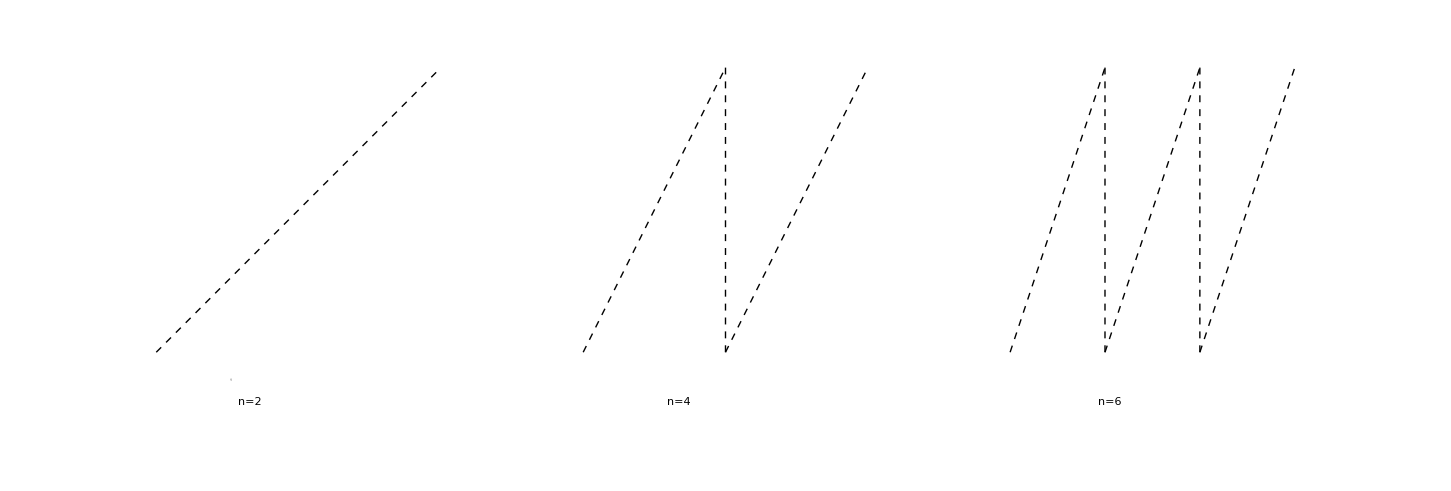

```mathematica
vertexSize=0.05;
edgeThickness=0.02;
isPurple[c1_,c2_]:=(
(ColorDistance[c1,Red]==0&&ColorDistance[c2,Blue]==0)
||
(ColorDistance[c1,Blue]==0&&ColorDistance[c2,Red]==0)
);
makeVertices[v_,colors_]:=(
n=Length[v];
Table[
Style[
Disk[v[[i]],vertexSize],
colors[[i]],
EdgeForm[Directive[Thick]]
],
{i,1,n}
]
);
makeEdges[e_,colors_,v_]:=(
n=Length[e];
Table[
With[
{a=e[[i]][[1]],b=e[[i]][[2]]},
Style[
Line[{v[[a]],v[[b]]}],
If[
isPurple[colors[[a]],colors[[b]]],
Lighter[Purple],
Black
],
Thickness[edgeThickness]
]
],
{i,1,n}
]
);
makeDissection[v_,colors_,e_]:=Graphics[
makeEdges[e,colors,v]
~Join~
makeVertices[v,colors]
];
```

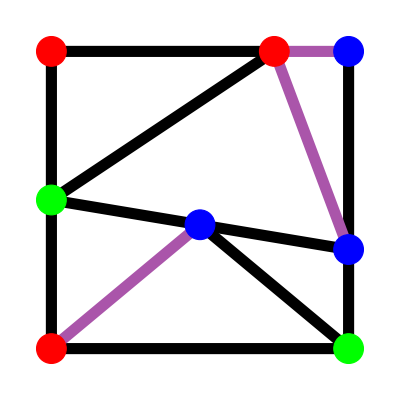

```mathematica
makeDissection[
{{0,0},{1,0},{0,1},{1,1},{0,1/2},{3/4,1},{1,1/3},{1/2,5/12}},
{Red,Green,Red,Blue,Green,Red,Blue,Blue},
{{1,5},{5,3},{3,6},{6,4},{4,7},{7,2},{2,1},{1,8},{8,2},{8,5},{8,7},{7,6},{6,5}}
]
```

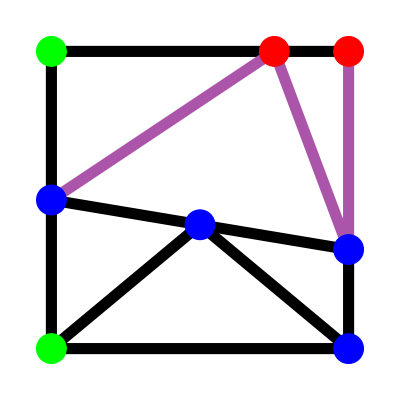

```mathematica
makeDissection[
{{0,0},{1,0},{0,1},{1,1},{0,1/2},{3/4,1},{1,1/3},{1/2,5/12}},
{Green,Blue,Green,Red,Blue,Red,Blue,Blue},
{{1,5},{5,3},{3,6},{6,4},{4,7},{7,2},{2,1},{1,8},{8,2},{8,5},{8,7},{7,6},{6,5}}
]
```

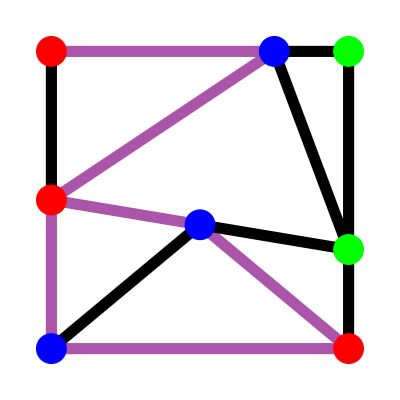

```mathematica
makeDissection[
{{0,0},{1,0},{0,1},{1,1},{0,1/2},{3/4,1},{1,1/3},{1/2,5/12}},
{Blue,Red,Red,Green,Red,Blue,Green,Blue},
{{1,5},{5,3},{3,6},{6,4},{4,7},{7,2},{2,1},{1,8},{8,2},{8,5},{8,7},{7,6},{6,5}}
]
```

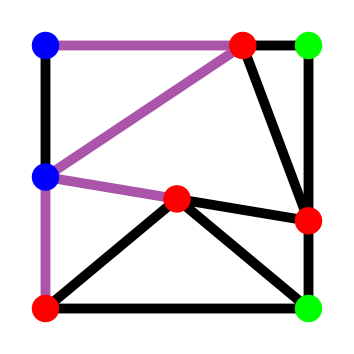

```mathematica
makeDissection[
{{0,0},{1,0},{0,1},{1,1},{0,1/2},{3/4,1},{1,1/3},{1/2,5/12}},
{Red,Green,Blue,Green,Blue,Red,Red,Red},
{{1,5},{5,3},{3,6},{6,4},{4,7},{7,2},{2,1},{1,8},{8,2},{8,5},{8,7},{7,6},{6,5}}
]
```

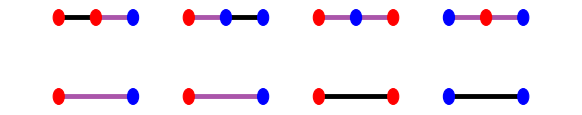

```mathematica
w=1.75;
h=-0.75;
edgeThickness=0.006;
vertexSize=0.075;
makeDissection[
Catenate[
Table[
{{a,0},{a+1/2,0},{a+1,0},{a,h},{a+1,h}},
{a,0,3w,w}
]
],
{
Red,Red,Blue,Red,Blue,
Red,Blue,Blue,Red,Blue,
Red,Blue,Red,Red,Red,
Blue,Red,Blue,Blue,Blue
},
Catenate[
Table[
{{i,i+1},{i+1,i+2},{i+3,i+4}},
{i,1,20,5}
]
]
]
```